```mathematica
p[x_, t_] := 1/(√(4 π d t)) ⅇ^(-x^2/(4 d t))
```

```mathematica
x = √(2d t) η
```

```mathematica
β = √(2 d t)
```

```mathematica
ρ[√(2 d t n)x] = 1/(√(2 d t n))1/π √(2 - x^2)
```

```mathematica
ρ[x_, t_] := (√(2 - x^2/(2 d t n)))/(π √(2 d t n))
```

```mathematica
Integrate[r ⅇ^(-r t)HeavisideTheta[4 d t n - x^2](√(2 - x^2/(2 d t n)))/(π √(2 d t n)), {t, 0, Infinity}, Assumptions->{d > 0, n > 0, x ∈ Reals, r > 0}]
```

ConditionalExpression[(r (2 ⅇ^(-(r x^2)/(4 d n)) √π √((d n)/r)+π Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))])))/(2 d n π), x≠0]

```mathematica
Integrate[r ⅇ^(-r t)(√2)/(π √(2 d t n)), {t, 0, Infinity}, Assumptions->{d > 0, n > 0, x ∈ Reals, r > 0}]
```

r/(√π √(d n r))

```mathematica
FullSimplify[(r (2 ⅇ^(-(r x^2)/(4 d n)) √π √((d n)/r)+π Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))])))/(2 d n π), Assumptions->{r > 0, d > 0, n > 0, x ∈ Reals}]
```

((2 ⅇ^(-(r x^2)/(4 d n)) √(d n r))/(√π)+r Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))]))/(2 d n)

```mathematica
Manipulate[Plot[(r (2 ⅇ^(-(r x^2)/(4 d n)) √π √((d n)/r)+π Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))])))/(2 d n π), {x, -10, 10}], {d, 1, 1}, {r, 0.1, 1000}, {n, 10, 1000}]
```

General::munfl: Exp[-1167.4] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Series[((2 ⅇ^(-(r x^2)/(4 d n)) √(d n r))/(√π)+r Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))]))/(2 d n), {r, 0, 3}]
```

(√(d n) √r)/(d n √π)-(Abs[x] r)/(2 (d n))+((-x^2+2 Abs[x]^2) r^(3/2))/(4 d n √(d n) √π)+((3 x^4-4 Abs[x]^4) r^(5/2))/(96 d^2 n^2 √(d n) √π)+O[r]^(7/2)

```mathematica
Integrate[((2 ⅇ^(-(r x^2)/(4 d n)) √(d n r))/(√π)-r Abs[x] Erfc[(r Abs[x])/(2 √(d n r))])/(2 d n), {x, -Infinity, Infinity}, Assumptions->{d > 0, n > 0, r > 0}]
```

1

```mathematica
FullSimplify[Erf[x]-1 ==  - Erfc[x]]
```

True

```mathematica
((2 ⅇ^(-(r x^2)/(4 d n)) √(d n r))/(√π)-r Abs[x] Erfc[(r Abs[x])/(2 √(d n r))])/(2 d n)
```

```mathematica
√(r/(4d n))x = z
```

```mathematica
ρ[z] =√(r/(4 d n)) (2 ⅇ^(-z^2)  -√(4π) Abs[z] Erfc[Abs[z]])/(√π)
```

```mathematica
Integrate[(2 ⅇ^(-z^2)  -√(4π) Abs[z] Erfc[Abs[z]])/(√π), {z, -Infinity, Infinity}]
```

1

```mathematica
Series[(2 ⅇ^(-z^2)  -√(4π) Abs[z] Erfc[Abs[z]])/(√π), {z, 0, 1}]
```

-2 Abs[z] Erfc[Abs[z]]+(2/(√π)+O[z]^2)

```mathematica
Asymptotic[(2 ⅇ^(-z^2)  -√(4π) Abs[z] Erfc[Abs[z]])/(√π), z -> Infinity]
```

$Aborted

```mathematica
Series[Erfc[z], {z, Infinity, 3}]
```

ⅇ^(-z^2+O[1/z]^4) (1/(√π z)-1/(2 √π z^3)+O[1/z]^4)

```mathematica
Asymptotic[ (ⅇ^(-z^2))/(√π z^2) , z -> Infinity]
```

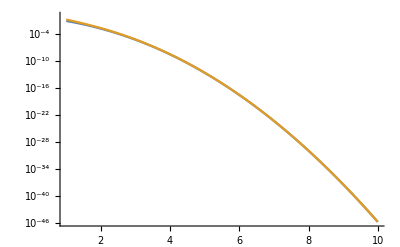

```mathematica
LogPlot[{(2 ⅇ^(-z^2)  -√(4π) Abs[z] Erfc[Abs[z]])/(√π), (ⅇ^(-z^2))/(√π z^2) }, {z, 1, 10}]
```

```mathematica
FullSimplify[Integrate[p[x, t] ⅇ^(-r t)r, {t, 0, Infinity}, Assumptions->{r > 0, x ∈ Reals, d > 0}], Assumptions->{r > 0, x ∈ Reals, d > 0}]
```

(ⅇ^(-√(r/d) Abs[x]) r)/(2 √(d r))

```mathematica
1+2+3+4+
```

```mathematica
Sum[n, {n, 1, i}]
```

1/2 i (1+i)

```mathematica
1/2  i(1+i)
```

```mathematica
Integrate[z^2/(√π)ⅇ^(-z^2), {z, -Infinity, Infinity}]
```

1/2

```mathematica
Series[Erfc[x], {x, 0, 1}]
```

1-(2 x)/(√π)+O[x]^2

```mathematica
-4 z^2/π+(2/(√π)+O[z]^2)
```

```mathematica
-2 Abs[z] Erfc[Abs[z]]+(2/(√π)+O[z]^2)
```

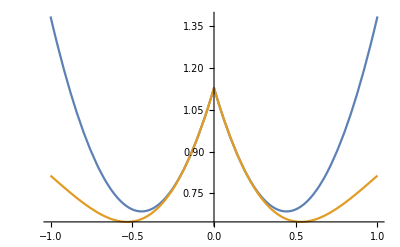

```mathematica
Plot[{2/(√π)-2 (Abs[z]- 2 z^2/(√π)), 2/(√π)-2 Abs[z] Erfc[Abs[z]]}, {z, -1, 1}]
```

```mathematica
-2 Abs[z] Erfc[Abs[z]]+(2/(√π)+O[z]^2)
```

```mathematica
Asymptotic[z Erfc[z], {z, 0, 2}]
```

z-(2 z^2)/(√π)

```mathematica
FullSimplify[2/(√π)(1 - z^2)- 2(Abs[z] - 2 z^2/(√π))]
```

(2 (1+z^2))/(√π)-2 Abs[z]

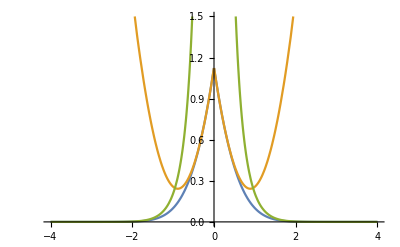

```mathematica
Plot[{(2 ⅇ^(-z^2)  -√(4π) Abs[z] Erfc[Abs[z]])/(√π), (2 (1+z^2))/(√π)-2 Abs[z], (ⅇ^(-z^2))/(√π z^2)}, {z, -4, 4}, PlotRange->{Automatic, {0, 1.5}}]
```

```mathematica
Integrate[r Exp[-1/t x2 - lnX - r t] t^(-n(n+1)/4), {t, 0, Infinity}, Assumptions->{r > 0, x2 > 0, n>0}]
```

2 ⅇ^-lnX r (r/x2)^(1/8 (-4+n+n^2)) BesselK[1/4 (-4+n+n^2),2 √(r x2)]

```mathematica
Manipulate[Plot[{ Log[1/((√(z^2))^(1-(n(n+1))/4)BesselK[(n(n+1))/4-1, √(z^2)])], -Log[(√(z^2))^(-n^2/2)√((2π)/n^2)((2ⅇ)/n^2)^(-n^2/4)]}, {z, -10, 10}], {n, 1, 100}]
```

```mathematica
Limit[Log[1/((√(z^2))^(1-(n(n+1))/4)BesselK[(n(n+1))/4-1, √(z^2)])], z -> 0, Assumptions->{n > 0}]
```

ConditionalExpression[-∞, n+n^2>4]

```mathematica
-Log[(√(z^2))^(-n^2/4)BesselK[n^2/4, √(z^2)]]
```

```mathematica
Limit[BesselK[n, x], n-> Infinity] = √(π/(2 n))((ⅇ z)/(2 n))^-n
```

lim_(n→∞) BesselK[n,x]

```mathematica
Manipulate[LogPlot[{BesselK[n, z], √(π/(2 n))((ⅇ z)/(2 n))^-n}, {z, 1, 10}], {n, 1, 100}]
```

```mathematica
-Log[(√(z^2))^(-n^2/2)√((2π)/n^2)((2ⅇ)/n^2)^(-n^2/4)]
```

```mathematica
n^2/2 Log[Abs[z]] - Log[√((2π)/n^2)((2ⅇ)/n^2)^(-n^2/4)]
```

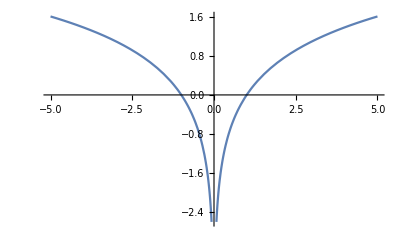

```mathematica
Plot[Log[Abs[z]], {z, -5, 5}]
```

```mathematica
Integrate[r ⅇ^(-r t)HeavisideTheta[4 d t n - x^2](√(2 - x^2/(2 d t n)))/(π √(2 d t n)), {t,T, Infinity}, Assumptions->{d > 0, n > 0, x ∈ Reals, r > 0, T> 0 }]
```

ConditionalExpression[(r (2 ⅇ^(-(r x^2)/(4 d n)) √π √((d n)/r)+π Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))])))/(2 d n π), 4 d n T<x^2]

```mathematica
Integrate[r ⅇ^(-r t)HeavisideTheta[4 d t n - x^2](√(2 - x^2/(2 d t n)))/(π √(2 d t n)), {t,0, Infinity}, Assumptions->{d > 0, n > 0, x ∈ Reals, r > 0 }]
```

ConditionalExpression[(r (2 ⅇ^(-(r x^2)/(4 d n)) √π √((d n)/r)+π Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))])))/(2 d n π), x≠0]

```mathematica
(r (2 ⅇ^(-(r x^2)/(4 d n)) √π √((d n)/r)+π Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))])))/(2 d n π) - (r (2 ⅇ^(-(r x^2)/(4 d n)) √π √((d n)/r)+π Abs[x] (-1+Erf[(r Abs[x])/(2 √(d n r))])))/(2 d n π)HeavisideTheta[x^2- 4 d n T]
```

```mathematica
x -> √((4 d n)/r)z
```

```mathematica
√(r/(4 d n))(2/(√π) ⅇ^(-z^2)  - 2Abs[z] Erfc[Abs[z]]HeavisideTheta[r T - z^2]+ (2 √(2 - (2 z^2)/(r T)))/(π √(2 r T)) ⅇ^(-r T))
```

```mathematica
Manipulate[Plot[2/(√π) ⅇ^(-z^2)  - 2Abs[z] Erfc[Abs[z]]HeavisideTheta[γ - z^2]+ (2 √(2 - (2 z^2)/γ))/(π √(2 γ)) ⅇ^-γ,{z, -√γ, √γ}], {γ, 0.001, 2}]
```